```mathematica
(* Load image *)
img=Image[-Graphics-];
```

```mathematica
(* Load palette *)
palette=Image[-Graphics-];
```

```mathematica
(* colors to numbers *)
palettelist=PixelValue[palette,{9,1;;}];
palettelist=palettelist⟦;;-4⟧;
palettelist=DeleteDuplicates[palettelist];

n=Length[palettelist];
palettelist⟦;;,4⟧=Table[i/n*200,{i,n}];(* range of values *)
PrependTo[palettelist,{1,1,1,0}];(* White region has zero events *)
```

```mathematica
dim=ImageDimensions[img];
nbins={12,20};
step=Round[dim/nbins];
xpt=Round/@Range[step⟦1⟧/2,dim⟦1⟧,step⟦1⟧];
ypt=Round/@Range[step⟦2⟧/2,dim⟦2⟧,step⟦2⟧];
```

```mathematica
Digitize[x_,y_]:=Block[{listofpoints=Flatten[Table[{i,j},{i,x},{j,y}],1],nearest,pos,pts,res},
pts=PixelValue[img,listofpoints]⟦;;,1;;3⟧;
nearest=Table[Nearest[palettelist⟦;;,{1,2,3}⟧,pts⟦i⟧]⟦1⟧,{i,Length@pts}];
pos=Table[Position[palettelist⟦;;,{1,2,3}⟧,nearest⟦i⟧]⟦1,1⟧,{i,Length@nearest}];
res=palettelist⟦#,4⟧&/@pos;
Table[Flatten@{listofpoints⟦i⟧,res⟦i⟧},{i,Length@res}]
]
(*Digitize[xpt,ypt]*)
tab=Partition[Digitize[xpt,ypt],nbins⟦2⟧];
```

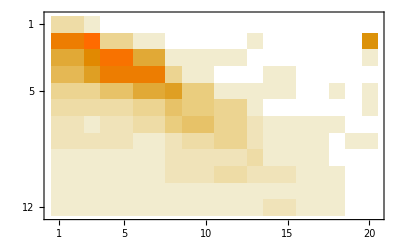

```mathematica
MatrixPlot[tab⟦;;,;;,3⟧]
```

```mathematica
Round@tab;
N@Total[Round@tab⟦;;,;;,3⟧,2]
```

5836.

```mathematica
N@Max[tab⟦;;,;;,3⟧]
```

192.308